Estimate the order of w_0

```mathematica
ClearAll;

inittime=AbsoluteTime[];

zero[x_]=0;

W=w0-A Exp[-a T]+B Exp[-b T]  X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];

vorder=50;

Block[{$MaxExtraPrecision=∞},

valA=1;
vala=4*Pi^2;
valB=0.1;
valb=4*Pi^2-10;

ret=1.0;
rex=Sqrt[3]-1;
Do[
valw0=SetPrecision[j*10^(-20),5];
veqntemp=V;

veqn=veqntemp*10^(vorder)/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};

Quiet[
solmin=FindMinimum[veqn,{{ReT,ret},{ReX,rex}},PrecisionGoal->100,AccuracyGoal->100,WorkingPrecision->5000,MaxIterations->1000,Method->"InteriorPoint"];
];

Print["w_0=",valw0,", V_min=",N[solmin[[1]],1]*10^(-vorder)];
,{j,1,100,1}];
];
```

w_0=1.×10^-20, V_min=-9.89457×10^-42

w_0=2.×10^-20, V_min=-4.14449×10^-41

w_0=3.×10^-20, V_min=-9.58312×10^-41

w_0=4.×10^-20, V_min=-1.73724×10^-40

w_0=5.×10^-20, V_min=-2.7561×10^-40

w_0=6.×10^-20, V_min=-4.0187×10^-40

w_0=7.×10^-20, V_min=-5.52825×10^-40

w_0=8.×10^-20, V_min=-7.28747×10^-40

w_0=9.×10^-20, V_min=-9.29875×10^-40

w_0=1.×10^-19, V_min=-1.15642×10^-39

w_0=1.1×10^-19, V_min=-1.40859×10^-39

w_0=1.2×10^-19, V_min=-1.68654×10^-39

w_0=1.3×10^-19, V_min=-1.99045×10^-39

w_0=1.4×10^-19, V_min=-2.32046×10^-39

w_0=1.5×10^-19, V_min=-2.67671×10^-39

w_0=1.6×10^-19, V_min=-3.05935×10^-39

w_0=1.7×10^-19, V_min=-3.46848×10^-39

w_0=1.8×10^-19, V_min=-3.90422×10^-39

w_0=1.9×10^-19, V_min=-4.3667×10^-39

w_0=2.×10^-19, V_min=-4.85601×10^-39

w_0=2.1×10^-19, V_min=-6.×10^269

w_0=2.2×10^-19, V_min=-4.06569×10^256

w_0=2.3×10^-19, V_min=-6.48594×10^-39

w_0=2.4×10^-19, V_min=-7.08355×10^-39

w_0=2.5×10^-19, V_min=-7.70846×10^-39

w_0=2.6×10^-19, V_min=-8.36075×10^-39

w_0=2.7×10^-19, V_min=-9.04049×10^-39

w_0=2.8×10^-19, V_min=-9.74778×10^-39

w_0=2.9×10^-19, V_min=-1.04827×10^-38

w_0=3.×10^-19, V_min=-1.12452×10^-38

w_0=3.1×10^-19, V_min=-1.20356×10^-38

w_0=3.2×10^-19, V_min=-1.28537×10^-38

w_0=3.3×10^-19, V_min=-1.36997×10^-38

w_0=3.4×10^-19, V_min=-1.45737×10^-38

w_0=3.5×10^-19, V_min=-1.54757×10^-38

w_0=3.6×10^-19, V_min=-1.64057×10^-38

w_0=3.7×10^-19, V_min=-1.73639×10^-38

w_0=3.8×10^-19, V_min=-1.83502×10^-38

w_0=3.9×10^-19, V_min=-1.93648×10^-38

w_0=4.×10^-19, V_min=-2.04077×10^-38

w_0=4.1×10^-19, V_min=-2.14789×10^-38

w_0=4.2×10^-19, V_min=-2.25785×10^-38

w_0=4.3×10^-19, V_min=-2.37066×10^-38

w_0=4.4×10^-19, V_min=-2.48632×10^-38

w_0=4.5×10^-19, V_min=-2.60483×10^-38

w_0=4.6×10^-19, V_min=-2.72621×10^-38

w_0=4.7×10^-19, V_min=-2.85044×10^-38

w_0=4.8×10^-19, V_min=-2.97755×10^-38

w_0=4.9×10^-19, V_min=-3.10753×10^-38

w_0=5.×10^-19, V_min=-3.24039×10^-38

w_0=5.1×10^-19, V_min=-3.37613×10^-38

w_0=5.2×10^-19, V_min=-3.51476×10^-38

w_0=5.3×10^-19, V_min=-3.65627×10^-38

w_0=5.4×10^-19, V_min=-3.80068×10^-38

w_0=5.5×10^-19, V_min=-3.948×10^-38

w_0=5.6×10^-19, V_min=-4.09821×10^-38

w_0=5.7×10^-19, V_min=-4.25133×10^-38

w_0=5.8×10^-19, V_min=-4.40736×10^-38

w_0=5.9×10^-19, V_min=-4.56631×10^-38

w_0=6.×10^-19, V_min=-4.72818×10^-38

w_0=6.1×10^-19, V_min=-4.89296×10^-38

w_0=6.2×10^-19, V_min=-5.06067×10^-38

w_0=6.3×10^-19, V_min=-5.23132×10^-38

w_0=6.4×10^-19, V_min=-5.40489×10^-38

w_0=6.5×10^-19, V_min=-5.5814×10^-38

w_0=6.6×10^-19, V_min=-5.76085×10^-38

w_0=6.7×10^-19, V_min=-5.94324×10^-38

w_0=6.8×10^-19, V_min=-6.12858×10^-38

w_0=6.9×10^-19, V_min=-6.31687×10^-38

w_0=7.×10^-19, V_min=-6.50811×10^-38

w_0=7.1×10^-19, V_min=-6.70231×10^-38

w_0=7.2×10^-19, V_min=-6.89947×10^-38

w_0=7.3×10^-19, V_min=-7.09959×10^-38

w_0=7.4×10^-19, V_min=-7.30267×10^-38

w_0=7.5×10^-19, V_min=-7.50873×10^-38

w_0=7.6×10^-19, V_min=-7.71775×10^-38

w_0=7.7×10^-19, V_min=-7.92975×10^-38

w_0=7.8×10^-19, V_min=-8.14473×10^-38

w_0=7.9×10^-19, V_min=-8.36269×10^-38

w_0=8.×10^-19, V_min=-8.58363×10^-38

w_0=8.1×10^-19, V_min=-8.80755×10^-38

w_0=8.2×10^-19, V_min=-9.03447×10^-38

w_0=8.3×10^-19, V_min=-9.26438×10^-38

w_0=8.4×10^-19, V_min=-9.49728×10^-38

w_0=8.5×10^-19, V_min=-9.73318×10^-38

w_0=8.6×10^-19, V_min=-9.97208×10^-38

w_0=8.7×10^-19, V_min=-1.0214×10^-37

w_0=8.8×10^-19, V_min=-1.04589×10^-37

w_0=8.9×10^-19, V_min=-1.07068×10^-37

w_0=9.×10^-19, V_min=-1.09577×10^-37

w_0=9.1×10^-19, V_min=-1.12117×10^-37

w_0=9.2×10^-19, V_min=-1.14686×10^-37

w_0=9.3×10^-19, V_min=-1.17286×10^-37

w_0=9.4×10^-19, V_min=-1.19916×10^-37

w_0=9.5×10^-19, V_min=-1.22576×10^-37

w_0=9.6×10^-19, V_min=-1.25266×10^-37

w_0=9.7×10^-19, V_min=-1.27987×10^-37

w_0=9.8×10^-19, V_min=-1.30738×10^-37

w_0=9.9×10^-19, V_min=-1.33519×10^-37

w_0=1.×10^-18, V_min=-1.36331×10^-37

$Aborted

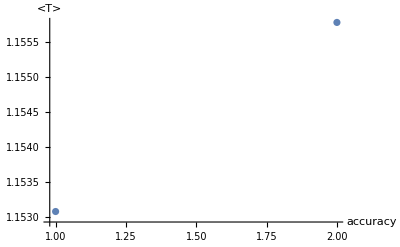

-Graphics-

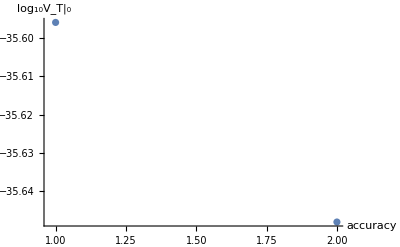

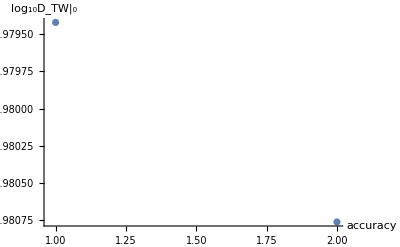

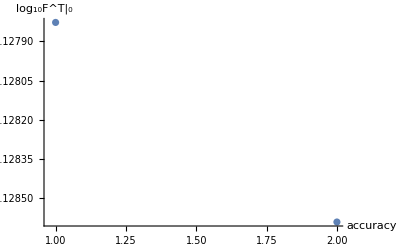

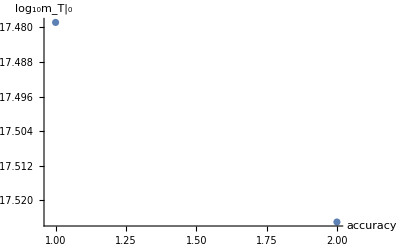

w_0=8.9×10^-19

<T>=1.155774999

<X>=0.8237318848

V|_0=1.×10^-60 minvtrue

(accuracy | w_0 | <T> | <X> | V|_0 | V_T|_0 | V_X|_0 | D_TW|_0 | F^T | F^X | m_T | m_(3/2)
1. | 9.×10^-19 | 1.153 | 0.8235 | 1.×10^-60 minvtrue | 3.×10^-36 | 6.5×10^-37 | -1.×10^-18 | 7.5×10^-19 | 6.5×10^-37 | 3.32×10^-18 | 3.6×10^-19
2. | 8.9×10^-19 | 1.156 | 0.8237 | 1.×10^-60 minvtrue | 2.25×10^-36 | 6.084×10^-37 | -1.045×10^-18 | 7.437×10^-19 | 6.084×10^-37 | 2.985×10^-18 | 3.545×10^-19)

time: 0時間0分19秒

```mathematica
ClearAll;

inittime=AbsoluteTime[];

zero[x_]=0;

W=w0-A Exp[-a T]+B Exp[-b T]  X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};

V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
vxeqn=FullSimplify[ComplexExpand[D[V,ReX]]];
vteqn=FullSimplify[ComplexExpand[D[V,ReT]]];
dtweqn=FullSimplify[ComplexExpand[DTW/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
fteqn=FullSimplify[ComplexExpand[-Exp[K/2](Subscript[invK, T T̄]*(OverBar[DTW])+Subscript[invK, T X̄]*(OverBar[DXW]))/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
fxeqn=FullSimplify[ComplexExpand[-Exp[K/2](Subscript[invK, X T̄]*(OverBar[DTW])+Subscript[invK, X X̄]*(OverBar[DXW]))/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
mteqn=FullSimplify[ComplexExpand[-Exp[K/2]*Subscript[invK, T T̄]*Subscript[W, TT]/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
m32eqn=FullSimplify[ComplexExpand[Exp[K/2]*W/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];

Block[{$MaxExtraPrecision=∞},

valA=1;
vala=4Pi^2;
valB=1;
valb=4Pi^2;
veqntemp=V;

ac=0;
vorder=60;
w0order=19;
doinit=1.0;

ret=1.0;rex=0.7;

list={{"accuracy","w_0","<T>","<X>","V|_0","V_T|_0","V_X|_0","D_TW|_0","F^T","F^X","m_T","m_(3/2)"}};

cnt=0;

While[ac<=69,
ac=ac+1;
Do[
cnt=cnt+1;
valw0=SetPrecision[(doinit+j*10^(-ac))*10^(-w0order),ac*2+1];
veqn=veqntemp*10^(vorder)/.{A->valA,a->vala,B->valB,w0->valw0,b->valb};

Quiet[
solmin=FindMinimum[veqn,{{ReT,ret},{ReX,rex}},PrecisionGoal->100,AccuracyGoal->100,WorkingPrecision->5000,MaxIterations->1000,Method->"InteriorPoint"];
];

minv=solmin[[1]];
If[minv<=0,Break[]];
minvtrue=solmin[[1]];

,{j,0,10,1}];

ret=ReT/.solmin[[2]];
rex=ReX/.solmin[[2]];

doinit=valw0*10^(w0order)-10^(-ac);

valvt=vteqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18),b->valb}/.{ReT->ret,ReX->rex};
valvx=vxeqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18),b->valb}/.{ReT->ret,ReX->rex};
valdtw=dtweqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18),b->valb}/.{ReT->ret,ReX->rex};
valft=fteqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18),b->valb}/.{ReT->ret,ReX->rex};
valfx=fxeqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18),b->valb}/.{ReT->ret,ReX->rex};
valmt=mteqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18),b->valb}/.{ReT->ret,ReX->rex};
valm32=m32eqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18),b->valb}/.{ReT->ret,ReX->rex};

list=Append[list,{ac,doinit*10^(-18),ret,rex,minvtrue*10^(-vorder),valvt,valvx,valdtw,valft,valvx,valmt,valm32}];
];
];

aclist=Table[list[[i,1]],{i,2,Length[list]}];

tlist=Table[list[[i,3]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],tlist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","<T>"}]];

vminloglist=Table[Log10[list[[i,5]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],vminloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10V|_0"}]];

vtloglist=Table[Log10[Abs[list[[i,6]]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],vtloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10V_T|_0"}]];

dtwloglist=Table[Log10[Abs[list[[i,8]]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],dtwloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10D_TW|_0"}]];

ftloglist=Table[Log10[list[[i,9]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],ftloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10F^T|_0"}]];

mtloglist=Table[Log10[list[[i,11]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],mtloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10m_T|_0"}]];

Print["w_0=",list[[Length[list],2]]];
Print["<T>=",N[list[[Length[list],3]],10]];
Print["<X>=",N[list[[Length[list],4]],10]];
Print["V|_0=",N[list[[Length[list],5]],10]];

Print[N[list,4]//MatrixForm];

time=AbsoluteTime[]-inittime;
hour=Floor[time/3600];
min=Floor[(time-hour*3600)/60];
sec=Floor[time-hour*3600-min*60];
Print["time: ",hour,"時間",min,"分",sec,"秒"];
```